```mathematica
Needs["NDSolve`FEM`"];
```

```mathematica
E1[X_,Y_,matrix_,fiber_,E1f_:70.0,E1m_:3.5]:=If[fiber/.{x->X,y->Y},E1f,If[matrix/.{x->X,y->Y},E1m,0]]
```

```mathematica
E2[X_,Y_,matrix_,fiber_,E2f_:70.0,E2m_:3.5]:=If[fiber/.{x->X,y->Y},E2f,If[matrix/.{x->X,y->Y},E2m,0]]
```

```mathematica
G12[X_,Y_,matrix_,fiber_,G12f_:29.2,G12m_:1.3]:=If[fiber/.{x->X,y->Y},G12f,If[matrix/.{x->X,y->Y},G12m,0]]
```

```mathematica
ν12[X_,Y_,matrix_,fiber_,ν12f_:0.2,ν12m_:0.4]:=If[fiber/.{x->X,y->Y},ν12f,If[matrix/.{x->X,y->Y},ν12m,0]]
```

```mathematica
ν23[X_,Y_,matrix_,fiber_,ν23f_:0.2,ν23m_:0.4]:=If[fiber/.{x->X,y->Y},ν23f,If[matrix/.{x->X,y->Y},ν23m,0]]
```

```mathematica
α1[X_,Y_,matrix_,fiber_,α1f_:4.7,α1m_:60.0]:=If[fiber/.{x->X,y->Y},α1f,If[matrix/.{x->X,y->Y},α1m,0]]
```

```mathematica
α2[X_,Y_,matrix_,fiber_,α2f_:4.7,α2m_:60.0]:=If[fiber/.{x->X,y->Y},α2f,If[matrix/.{x->X,y->Y},α2m,0]]
```

```mathematica
defineSingleRVE[Rf_,Vff_,θ_,Δθ_,a_]:=With[{l=0.5*Rf*Sqrt[Pi/Vff],ϕ=0,Δϕ=Δθ,ω=θ},With[{xA=Rf*Cos[ϕ-Δϕ],yA=Rf*Sin[ϕ-Δϕ],xB=Rf*Cos[ϕ+Δϕ],yB=Rf*Sin[ϕ+Δϕ]},With[{xC=0.5*(xA+xB),yC=0.5*(yA+yB),b=0.5*Sqrt[(xA-xB)^2+(yA-yB)^2]},With[{Δ=Sqrt[(Rf*Cos[ϕ]-xC)^2+(Rf*Sin[ϕ]-yC)^2],γ=ArcTan[xA-xC,yA-yC],δ=ArcTan[xB-xC,yB-yC]},With[{r=Δ+a},{x^2+y^2≤ Rf^2,-l≤x≤l&&-l≤y≤l&&x^2+y^2≥ Rf^2&&((Cos[ω]*x+Sin[ω]*y-xC)/r)^2+((-Sin[ω]*x+Cos[ω]*y-yC)/b)^2≥ 1,((Cos[ω]*x+Sin[ω]*y-xC)/r)^2+((-Sin[ω]*x+Cos[ω]*y-yC)/b)^2≤1&&x^2+y^2≥Rf^2}]]]]]
```

```mathematica
Manipulate[With[{xA=Rf*Cos[θf Degree-Δθf Degree],yA=Rf*Sin[θf Degree-Δθf Degree],xB=Rf*Cos[θf Degree+Δθf Degree],yB=Rf*Sin[θf Degree+Δθf Degree]},With[{xC=0.5*(xA+xB),yC=0.5*(yA+yB),b=0.5*Sqrt[(xA-xB)^2+(yA-yB)^2]},With[{Δ=Sqrt[(Rf*Cos[θf Degree]-xC)^2+(Rf*Sin[θf Degree]-yC)^2],γ=ArcTan[xA-xC,yA-yC],δ=ArcTan[xB-xC,yB-yC]},With[{r=Δ+af},Graphics[{Circle[{0,0},Rf],Rotate[Circle[{xC,yC},{b,r},{Pi,2*Pi}],Pi/2+θf Degree,{xC,yC}],Line[{{0,0},{xB,yB}}],Line[{{0,0},{xA,yA}}],Red,Line[{{xC,yC},{xC+Δ*Cos[θf Degree],yC+Δ*Sin[θf Degree]}}],Line[{{xA,yA},{xB,yB}}],Thick,Blue,Point[{{xA,yA},{xB,yB},{xC,yC}}]},Axes->True,AxesOrigin->{0,0},AxesLabel->{x,y},PlotRange->{{-1.5*l,1.5*l},{-1.5*l,1.5*l}},ImageSize->{ImgSize,ImgSize}]]]]],Control[{{θf,30 ,"θ"},-10*360,10*360,0.01}],Control[{{Δθf,10,"Δθ"},0,360,0.01}],Control[{{af,0.25,"Radial Crack Aperture"},0,1,0.0001}],Control[{{ImgSize,500,"ImageSize"},50,1000,50}]]
```

```mathematica
Rf=1;
Vff=0.6;
θ=40 Degree;
Δθ=10 Degree;
a=0.01;
```

```mathematica
l=0.5*Rf*Sqrt[Pi/Vff];
```

```mathematica
{fiber,matrix,crack}=defineSingleRVE[Rf,Vff,θ,Δθ,a];
```

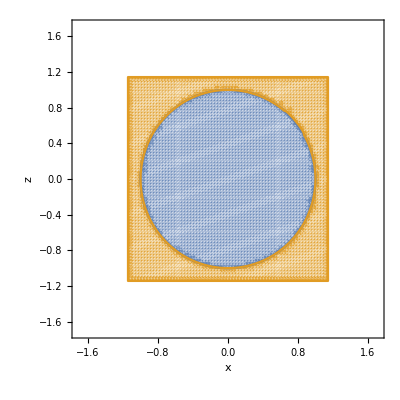

```mathematica
r=RegionPlot[{fiber,matrix},{x,-1.5*l,1.5*l},{y,-1.5*l,1.5*l},PlotPoints->100,MaxRecursion->3,Axes->True,AxesOrigin->{0,0},AxesLabel->{x,z}]
```

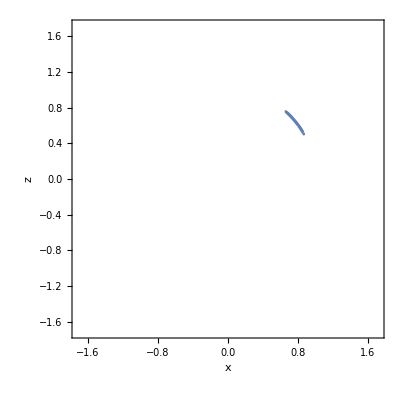

```mathematica
r2=RegionPlot[crack,{x,-1.5*l,1.5*l},{y,-1.5*l,1.5*l},PlotPoints->100,MaxRecursion->3,Axes->True,AxesOrigin->{0,0},AxesLabel->{x,z}]
```

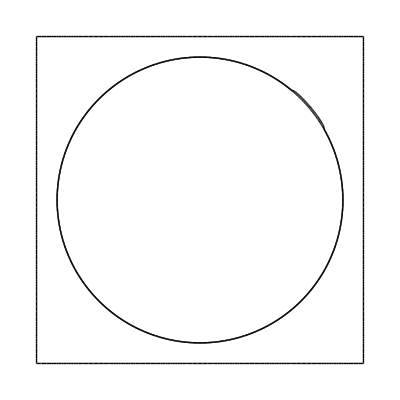

```mathematica
bmesh=ToBoundaryMesh["Coordinates"->Round[#,0.0001]&@First@Cases[r,GraphicsComplex[v_,___]:>v,∞],"BoundaryElements"->Cases[r,Line[p_,___]:>LineElement@Partition[p,2,1],∞]];
bmesh@"Wireframe"
```

```mathematica
mesh=ToElementMesh[bmesh,MeshQualityGoal->"Maximal",MaxCellMeasure->.1,"NodeReordering"->True];
mesh["Wireframe"]
```

-Graphics-

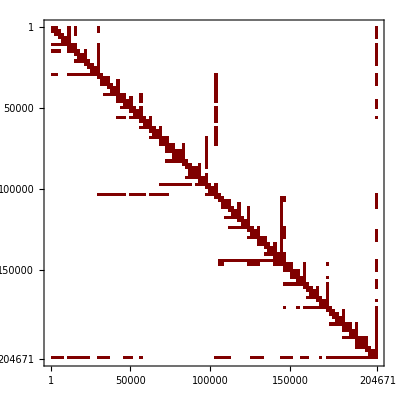

```mathematica
inci=Join@@ElementIncidents[mesh["MeshElements"]];
saPos=Flatten[ Map[ Outer[ List,#,#]&,inci], 2];
MatrixPlot[SparseArray[saPos->_]]
```

```mathematica
Length[mesh["Coordinates"]]
```

204671

```mathematica
Length[mesh["MeshElements"][[1,1]]]
```

101684

```mathematica
numReg=ToNumericalRegion[mesh];
```

```mathematica
ℒ1=-Laplacian[u[t,x,y],{x,y}];
```

```mathematica
ℒ2=-Laplacian[v[t,x,y],{x,y}];
```

```mathematica
pde1 = D[u[t,x,y],t]+d1[Rf]*ℒ1+d2[Rf]*ℒ2==0;
```

```mathematica
pde2 = D[v[t,x,y],t]+d1[Rf]*ℒ1+d2[Rf]*ℒ2==0;
```

```mathematica
Γint=DirichletCondition[u[t,x,y]-v[t,x,y]==0,(x^2+y^2==Rf^2&&!( θ-Δθ)≤ArcTan[x,y]≤ (θ+Δθ))];
```

```mathematica
Γext=DirichletCondition[v[t,x,y]==0,(x==-l ||x==l||y==-l ||y==l)];
```

```mathematica
{state}=NDSolve`ProcessEquations[{pde1,pde2,Γint,Γext,u[0,x,y]==0,v[0,x,y]==0},{u,v},{t,0,1},{x,y}∈numReg];
```

NDSolve`ProcessEquations::fembdcc: Cross-coupling of dependent variables in DirichletCondition[u-v==0,x^2+y^2==1&&!20 °≤ArcTan[x,y]≤40 °] is not supported in this version.

Set::shape: Lists {state} and «1» are not the same shape.

NDSolve`ProcessEquations::fembdcc: Cross-coupling of dependent variables in DirichletCondition[u-v==0,x^2+y^2==1&&!20 °≤ArcTan[x,y]≤40 °] is not supported in this version.

```mathematica
ℒ=-Laplacian[u[x,y],{x,y}];
```

```mathematica
{eigvalℛ1ℛ2,eigfuncℛ1ℛ2}=With[{Rf=1,Vff=0.6,θ=30 Degree,Δθ=10 Degree,n=6},With[{l=0.5*Rf*Sqrt[Pi/Vff],ℒ1=-If[x^2+y^2≤Rf^2,1,0]*Laplacian[u[x,y],{x,y}],ℒ2=-If[x^2+y^2≥ Rf^2,1,0]*Laplacian[v[x,y],{x,y}]},With[{Ω=Rectangle[{-l,l},{l,l}]},NDEigensystem[{ℒ1+ℒ2,DirichletCondition[u[x,y]==v[x,y],(x^2+y^2==Rf^2&&!( θ-Δθ)≤ArcTan[x,y]≤ (θ+Δθ))],DirichletCondition[v[x,y]==0,(x==-l ||x==l||y==-l ||y==l)]},{u[x,y],v[x,y]},{x,y}∈Ω,n]]]];With[{Rf=1,Vff=0.6,n=6},With[{l=0.5*Rf*Sqrt[Pi/Vff]},With[{Ω=Rectangle[{-l,l},{l,l}]},Grid[Partition[Table[Show[{ContourPlot[eigfuncℛ1ℛ2[[j]],{x,y}∈ℛ2,Frame->None,PlotPoints->60,PlotRange->Full,PlotLabel->eigvalℛ1ℛ2[[j]]],RegionPlot[Ω,PlotStyle->None,BoundaryStyle->{Black,Thick}]}],{j,1,Length[eigvalℛ1ℛ2]}],3]]]]]
```

Set::shape: Lists {eigvalℛ1ℛ2,eigfuncℛ1ℛ2} and NDEigensystem[{-If[Power[«2»]+Power[«2»]≤1,1,0] (u^(0,2)[x,y]+u^(2,0)[x,y])-If[Power[«2»]+Power[«2»]≥1,1,0] (v^(0,2)[x,y]+v^(2,0)[x,y]),DirichletCondition[u[x,y]==v[x,y],x^2+y^2==1&&!20 °≤ArcTan[x,y]≤40 °],DirichletCondition[v[x,y]==0,x==-1.14411||x==1.14411||y==-1.14411||y==1.14411]},{u[x,y],v[x,y]},{x,y}∈Rectangle[{-1.14411,1.14411},{1.14411,1.14411}],6] are not the same shape.

```mathematica
With[{Rf=1,Vff=0.6,θ=30 Degree,Δθ=10 Degree,n=6},With[{l=0.5*Rf*Sqrt[Pi/Vff],ℒ1=-If[x^2+y^2≤Rf^2,1,0]*Laplacian[u[x,y],{x,y}],ℒ2=-If[x^2+y^2≥ Rf^2,1,0]*Laplacian[v[x,y],{x,y}]},With[{Ω=Rectangle[{-l,l},{l,l}]},NDEigensystem[{ℒ1,ℒ2,DirichletCondition[u[x,y]==v[x,y],(x^2+y^2==Rf^2&&!( θ-Δθ)≤ArcTan[x,y]≤ (θ+Δθ))],DirichletCondition[v[x,y]==0,(x==-l ||x==l||y==-l ||y==l)]},{u[x,y],v[x,y]},{x,y}∈Ω,n]]]]
```

NDEigensystem[{-If[x^2+y^2≤1,1,0] (u^(0,2)[x,y]+u^(2,0)[x,y]),-If[x^2+y^2≥1,1,0] (v^(0,2)[x,y]+v^(2,0)[x,y]),DirichletCondition[u[x,y]==v[x,y],x^2+y^2==1&&!20 °≤ArcTan[x,y]≤40 °],DirichletCondition[v[x,y]==0,x==-1.14411||x==1.14411||y==-1.14411||y==1.14411]},{u[x,y],v[x,y]},{x,y}∈Rectangle[{-1.14411,1.14411},{1.14411,1.14411}],6]

```mathematica
Ω1=Rectangle[{-l,-l},{l,l}];
```

```mathematica
Ω2=RegionDifference[Rectangle[{-l,-l},{l,l}],Circle[{0,0},Rf,{θ-Δθ,θ+Δθ}]];
```

```mathematica
{eigvalℛ2,eigfuncℛ2}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Ω1,6];
Grid[Partition[Table[Show[{ContourPlot[eigfuncℛ2[[j]],{x,y}∈Ω1,Frame->None,PlotPoints->60,PlotRange->Full,PlotLabel->eigvalℛ2[[j]]],RegionPlot[Ω1,PlotStyle->None,BoundaryStyle->{Black,Thick}]}],{j,1,Length[eigvalℛ2]}],3]]
```

-Graphics-

```mathematica
{eigvalℛ2,eigfuncℛ2}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Ω2,6];
Grid[Partition[Table[Show[{ContourPlot[eigfuncℛ2[[j]],{x,y}∈Ω2,Frame->None,PlotPoints->60,PlotRange->Full,PlotLabel->eigvalℛ2[[j]]],RegionPlot[Ω2,PlotStyle->None,BoundaryStyle->{Black,Thick}]}],{j,1,Length[eigvalℛ2]}],3]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
{eigvalℛ2,eigfuncℛ2}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,!((theta-deltatheta)≤ ArcTan[x,y]≤ (theta+deltatheta))]},u[x,y],{x,y}∈ℛ2,6];
Grid[Partition[Table[Show[{ContourPlot[eigfuncℛ2[[j]],{x,y}∈ℛ2,Frame->None,PlotPoints->60,PlotRange->Full,PlotLabel->eigvalℛ2[[j]]],RegionPlot[ℛ2,PlotStyle->None,BoundaryStyle->{Black,Thick}]}],{j,1,Length[eigvalℛ2]}],3]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
{eigvalℛ1,eigfuncℛ1}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,!((x^2+y^2==Rf^2)&&(theta-deltatheta)≤ ArcTan[x,y]≤ (theta+deltatheta))]},u[x,y],{x,y}∈ℛ1,9,Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}}];
Grid[Partition[Table[Show[{ContourPlot[eigfuncℛ1[[j]],{x,y}∈ℛ1,Frame->None,PlotPoints->60,PlotRange->Full,PlotLabel->eigvalℛ1[[j]]],RegionPlot[ℛ1,PlotStyle->None,BoundaryStyle->{Black,Thick}]}],{j,1,Length[eigvalℛ1]}],3]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-